```mathematica
"Michaels Reconstructions";
```

```mathematica
"Mathematica Preliminaries";
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/Projects/CurrentProjects/IlgenfritzProjects/SpectralAnalysisOctober2016

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ErrorBarLogPlots`"]
```

```mathematica
CreateDirectory["./MichaelIlgenfritzAnalysisNovember2016"];
```

```mathematica
BLANK=" ";
```

```mathematica
"Lattice Setups";
```

```mathematica
(*afm[b_]:=Switch[b,1.90,0.0863,1.95, 0.0779,2.10, 0.0607];*)
```

```mathematica
(*am1GeV[b_]:=Switch[b,1.90,0.197/0.0863,1.95, 0.197/0.0779,2.10, 0.197/0.0607];*)
```

```mathematica
afm[b_]:=Switch[b,1.90,0.0936,1.95, 0.0823,2.10, 0.0646];
```

```mathematica
am1GeV[b_]:=Switch[b,1.90,0.197/0.0936,1.95, 0.197/0.0823,2.10, 0.197/0.0646];
```

```mathematica
BetaLatVals={1.90,1.90,1.90,1.90,1.90,1.90,1.90,1.95 ,1.95 ,1.95 ,1.95 ,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10}
```

{1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.95,1.95,1.95,1.95,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1}

```mathematica
Length[BetaLatVals]
```

21

```mathematica
BetaLatValsP=SetPrecision[{1.90,1.90,1.90,1.90,1.90,1.90,1.90,1.95 ,1.95 ,1.95 ,1.95 ,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10,2.10},3]
```

{1.9,1.9,1.9,1.9,1.9,1.9,1.9,1.95,1.95,1.95,1.95,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1,2.1}

```mathematica
NtVals={4,6,8,9,10,12,14,10,11,12,14,4,6,8,10,11,12,14,16,18,20};
```

```mathematica
NxVals={24,24,24, 24,24,24,32,32,32,32,32,32,32,32,32,32,32,32,32,40,48};
```

```mathematica
Temp=Table[am1GeV[BetaLatVals[[k]]]/NtVals[[k]],{k,1,Length[BetaLatVals]}]
```

{0.526175,0.350783,0.263088,0.233856,0.21047,0.175392,0.150336,0.239368,0.217607,0.199473,0.170977,0.762384,0.508256,0.381192,0.304954,0.277231,0.254128,0.217824,0.190596,0.169419,0.152477}

```mathematica
BetaVals=N[SetPrecision[1/Temp,4],4]
```

{1.901,2.851,3.801,4.276,4.751,5.702,6.652,4.178,4.595,5.013,5.849,1.312,1.968,2.623,3.279,3.607,3.935,4.591,5.247,5.903,6.558}

```mathematica
MinTmpAll=Min[Temp];
```

```mathematica
Sort[Temp]
```

{0.150336,0.152477,0.169419,0.170977,0.175392,0.190596,0.199473,0.21047,0.217607,0.217824,0.233856,0.239368,0.254128,0.263088,0.277231,0.304954,0.350783,0.381192,0.508256,0.526175,0.762384}

```mathematica
MaxTmpAll=Sort[Temp][[Length[Temp]-1]]
```

0.526175

```mathematica
(Temp[[Range[7,3,-1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll)
```

{0.,0.0666667,0.16,0.222222,0.3}

```mathematica
"Read in the correlators";
```

```mathematica
RawCorrelators=Table[If[FileExistsQ[ToString@StringForm["./DATAFILES/b``/NT``_NX``/MEASUREMENTS-LIN-NOCUT-AVG/full_gluon_avg.dat",BetaLatValsP[[k]],NtVals[[k]],NxVals[[k]] ]],Import[ToString@StringForm["./DATAFILES/b``/NT``_NX``/MEASUREMENTS-LIN-NOCUT-AVG/full_gluon_avg.dat",BetaLatValsP[[k]],NtVals[[k]],NxVals[[k]] ]],Print["Not Found" ,ToString@StringForm["./DATAFILES/b``/NT``_NX``/MEASUREMENTS-LIN-NOCUT-AVG/full_gluon_avg.dat",BetaLatValsP[[k]],NtVals[[k]],NxVals[[k]] ]]],{k,1,Length[BetaLatVals]}];
```

```mathematica
Clear[TransversalProcessed]
```

```mathematica
(*TransversalProcessed=Table[Table[{RawCorrelators[[j]][[k,6]],(2*Pi/BetaVals[[j]])*If[RawCorrelators[[j]][[k,6]]<=NtVals[[j]]/2,RawCorrelators[[j]][[k,6]],(-NtVals[[j]])+RawCorrelators[[j]][[k,6]]],RawCorrelators[[j]][[k,1]],RawCorrelators[[j]][[k,2]]*am1GeV[BetaLatVals[[j]]],(RawCorrelators[[j]][[k,7]]*NtVals[[j]]/BetaVals[[j]])^2+(RawCorrelators[[j]][[k,2]]*am1GeV[BetaLatVals[[j]]])^2,  RawCorrelators[[j]][[k,14]], RawCorrelators[[j]][[k,15]] },{k,1,Length[RawCorrelators[[j]]] }],{j,1,Length[BetaLatVals]}];*)
```

```mathematica
TransversalProcessed=Table[Table[{RawCorrelators[[j]][[k,6]],RawCorrelators[[j]][[k,7]]*am1GeV[BetaLatVals[[j]]],RawCorrelators[[j]][[k,1]],RawCorrelators[[j]][[k,2]]*am1GeV[BetaLatVals[[j]]],(RawCorrelators[[j]][[k,7]]*NtVals[[j]]/BetaVals[[j]])^2+(RawCorrelators[[j]][[k,2]]*am1GeV[BetaLatVals[[j]]])^2,  RawCorrelators[[j]][[k,12]], RawCorrelators[[j]][[k,13]] },{k,1,Length[RawCorrelators[[j]]] }],{j,1,Length[BetaLatVals]}];
```

```mathematica
MyColorScheme="DeepSeaColors";
```

```mathematica
"Test O(4) symmetry for b=2.10";
```

```mathematica
InterpolatedMu0=Table[Interpolation[TransversalProcessed[[b]][[Flatten@Position[TransversalProcessed[[b]][[All,1]],0],{4,6}]][[1;;]] ],{b,12,19}]
```

{InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…],InterpolatingFunction[…]}

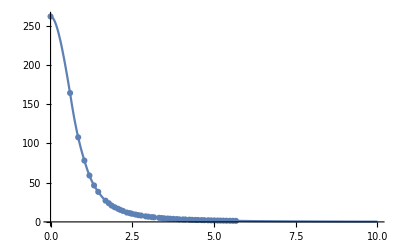

```mathematica
Show[ListPlot[TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],0],{4,6}]][[1;;50]],PlotRange->{{0,10},All}], Plot[InterpolatedMu0[[6]][x],{x,0,10},PlotRange->All]]
```

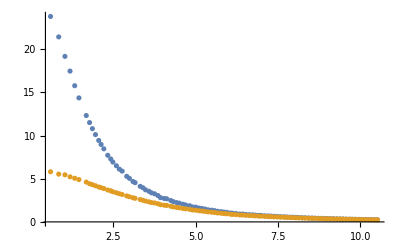

```mathematica
Show[ListPlot[{TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],1],{4,6}]],TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],2],{4,6}]]},PlotRange->All],Plot[InterpolatedMu0[[6]][Sqrt[]],{x,0,0.6},PlotRange->All]]
```

```mathematica
Table[TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,3]],l],{2,4,6}]],{l,DeleteDuplicates[TransversalProcessed[[17]][[All,3]]][[2;;2]]}]
```

{{{0.,0.597814,164.40000344945264033},{1.57856,0.597814,23.800616217753550075},{3.04954,0.597814,5.8108798472893345988},{4.31269,0.597814,2.5008281397562415194},{5.28195,0.597814,1.436321418731359767},{5.89125,0.597814,1.0409506273327950865},{6.09907,0.597814,0.95562148622657483443},{-5.89125,0.597814,1.0526437573677005499},{-5.28195,0.597814,1.4220179821044596213},{-4.31269,0.597814,2.4883672809487262789},{-3.04954,0.597814,5.8073857043117751431},{-1.57856,0.597814,24.346416723425562623}}}

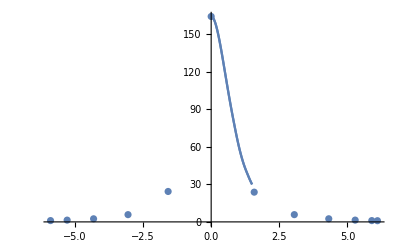

```mathematica
Show[ListPlot[Table[TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,3]],l],{2,6}]],{l,DeleteDuplicates[TransversalProcessed[[17]][[All,3]]][[2;;2]]}],PlotRange->All],Plot[InterpolatedMu0[[6]][Sqrt[0.5978135184186846^2+x^2]],{x,0,1.5},PlotRange->All],Plot[InterpolatedMu0[[6]][Sqrt[0.5978135184186846^2+x^2]],{x,0,1.5},PlotRange->All]]
```

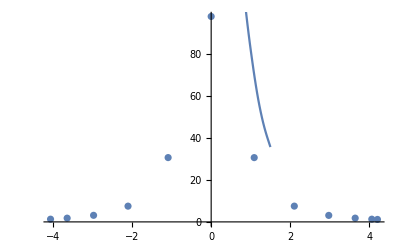

```mathematica
Show[ListPlot[Table[TransversalProcessed[[6]][[Flatten@Position[TransversalProcessed[[6]][[All,3]],l],{2,6}]],{l,DeleteDuplicates[TransversalProcessed[[6]][[All,3]]][[2;;2]]}],PlotRange->All],Plot[InterpolatedMu0[[6]][Sqrt[0.11435949633086609^2+x^2]],{x,0,1.5},PlotRange->All]]
```

```mathematica
TransversalProcessed[[6]][[Flatten@Position[TransversalProcessed[[6]][[All,1]],1],{4,2,6}]][[1;;2]]
```

{{0.549437,1.08947,30.663212945705819124},{0.777022,1.08947,24.841920081080910876}}

```mathematica
2*Pi*0.1902
```

1.19506

```mathematica
TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],1],{2,4,6}]][[1;;3]]
```

{{1.57856,0.597814,23.800616217753550075},{1.57856,0.845436,21.431915413471060106},{1.57856,1.03544,19.175576401968836393}}

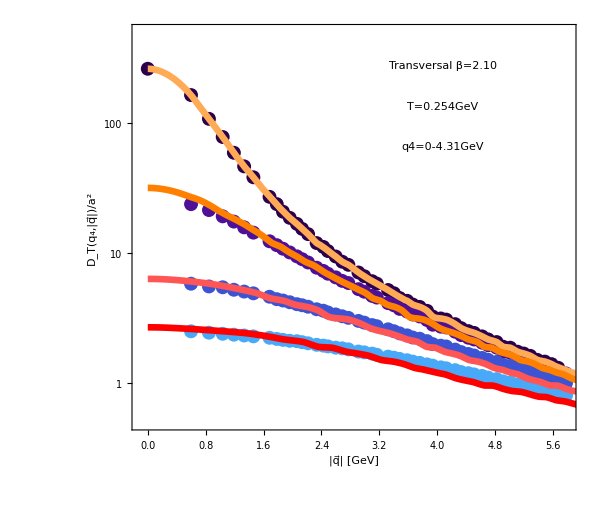

```mathematica
MyColorScheme="DeepSeaColors";X=Show[ListLogPlot[{TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],0],{4,6}]][[1;;50]],TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],1],{4,6}]][[1;;50]],TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],2],{4,6}]][[1;;50]],TransversalProcessed[[17]][[Flatten@Position[TransversalProcessed[[17]][[All,1]],3],{4,6}]][[1;;50]]},PlotRange->{{-0.1,5.8},{0.5,500}},Frame->{True,True,False,False},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/4]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[17]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[17]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[17]][[5,2]],3]    ],Scaled[{0.7,0.7}]]},22]], LogPlot[InterpolatedMu0[[6]][x],{x,0,6},PlotRange->All,PlotStyle->{Lighter[Orange],Thickness[0.008]}],LogPlot[InterpolatedMu0[[6]][Sqrt[x^2+(1.5785557859194093)^2]],{x,0,6},PlotRange->All,PlotStyle->{Orange,Thickness[0.008]}],LogPlot[InterpolatedMu0[[6]][Sqrt[x^2+(3.0495356037151593)^2]],{x,0,6},PlotRange->All,PlotStyle->{Lighter[Red],Thickness[0.008]}],LogPlot[InterpolatedMu0[[6]][Sqrt[x^2+(4.312694609713638)^2]],{x,0,6},PlotRange->All,PlotStyle->{Red,Thickness[0.008]}]]
```

```mathematica
Export["B210CorrTransVerifyScaling1.pdf",X]
```

B210CorrTransVerifyScaling1.pdf

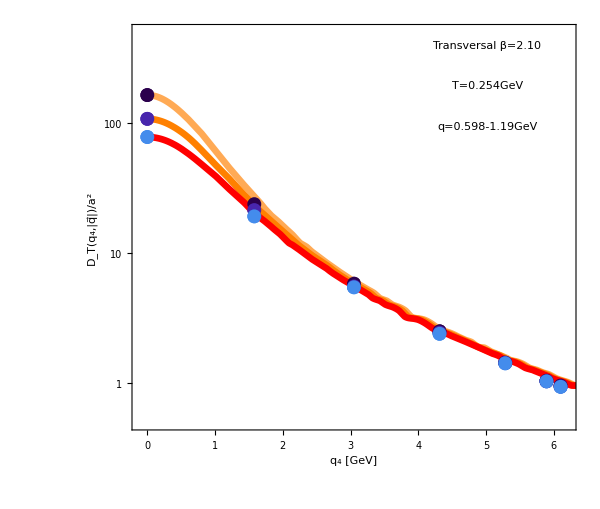

```mathematica
CurBeta=17;
MyColorScheme="DeepSeaColors";Y=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;4]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,6.2},{0.5,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/3]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[4]],4]],3]    ],Scaled[{0.8,0.75}]]},22]];X=Show[Y,LogPlot[InterpolatedMu0[[6]][Sqrt[0.5978135184186846^2+x^2]],{x,0,10},PlotRange->All,PlotStyle->{Lighter[Orange],Thickness[0.008]}],LogPlot[InterpolatedMu0[[6]][Sqrt[0.8454359855176758^2+x^2]],{x,0,10},PlotRange->All,PlotStyle->{Orange,Thickness[0.008]}],LogPlot[InterpolatedMu0[[6]][Sqrt[1.0354433873526747^2+x^2]],{x,0,10},PlotRange->All,PlotStyle->{Red,Thickness[0.008]}],Y]
```

```mathematica
Export["B210CorrTransVerifyScaling2.pdf",X]
```

B210CorrTransVerifyScaling2.pdf

```mathematica
"b=1.90";
```

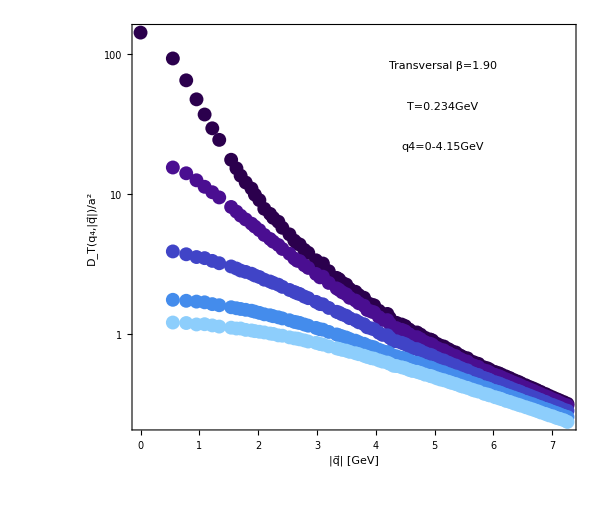

```mathematica
CurBeta=4;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B190CorrTransHighTVspMultiMu.pdf",X]
```

B190CorrTransHighTVspMultiMu.pdf

```mathematica
"B190CorrTransHighTVspMultiMu.pdf"
```

B190CorrTransHighTVspMultiMu.pdf

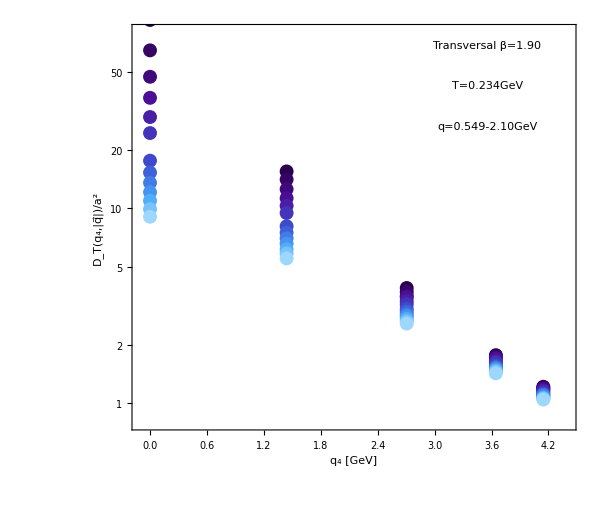

```mathematica
CurBeta=4;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,4.4},{0.8,80}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B190CorrTransHighTVsmuMultiP.pdf",X]
```

B190CorrTransHighTVsmuMultiP.pdf

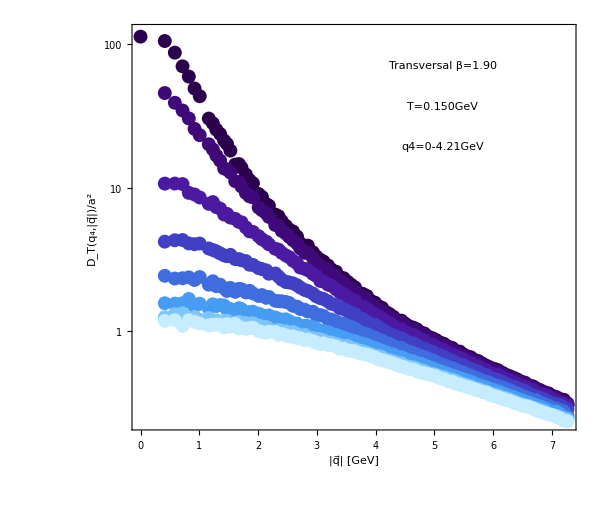

```mathematica
CurBeta=7;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotRange->All,PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B190CorrTransLowTVspMultiMu.pdf",X]
```

B190CorrTransLowTVspMultiMu.pdf

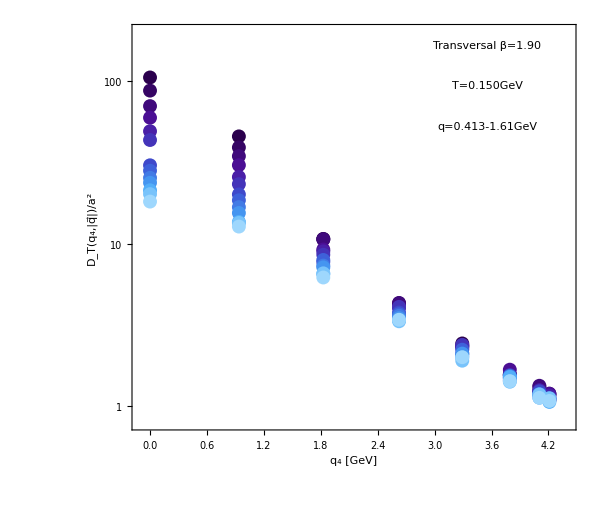

```mathematica
CurBeta=7;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,4.4},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B190CorrTransLowTVsmuMultiP.pdf",X]
```

B190CorrTransLowTVsmuMultiP.pdf

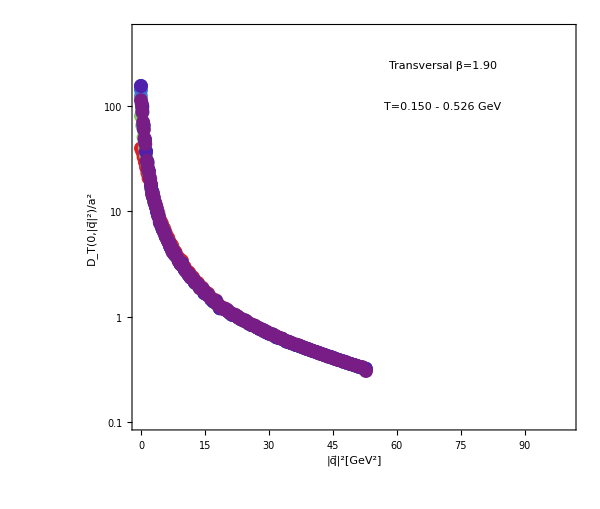

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Table[TransversalProcessed[[b]][[Flatten@Position[TransversalProcessed[[b]][[All,1]],0],{5,6,7}]],{b,1,7}],Frame->{True,True,False,False},PlotRange->{{-0.1,100},{0.1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[1,7,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗|^2[GeV^2]","D_T(0,|q⃗|^2)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[7]],3],SetPrecision[Temp[[1]],3]  ],Scaled[{0.7,0.8}]]},22]]
```

```mathematica
Export["B190CorrTransVsp2MultiT.pdf",X]
```

B190CorrTransVsp2MultiT.pdf

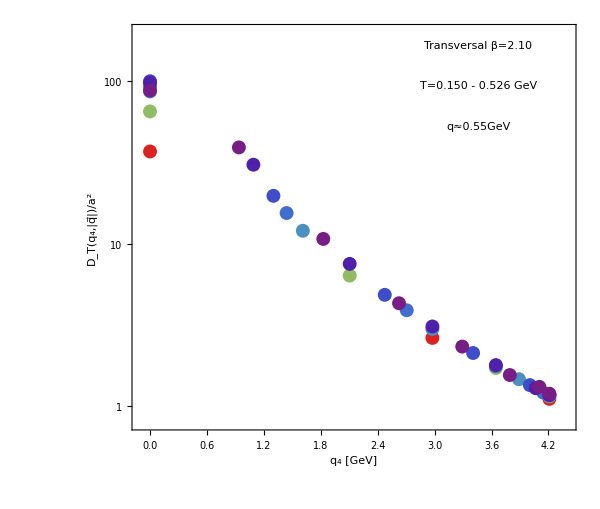

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[If[CurBeta≠7,2,3];;If[CurBeta≠7,2,3]]]}],{CurBeta,1,7}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,4.4},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[1,7,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[12]]],Scaled[{0.78,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[7]],3],SetPrecision[Temp[[1]],3]  ],Scaled[{0.78,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[1]][[Table[Min[Flatten@Position[TransversalProcessed[[1]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[1]][[All,3]]][[2;;]]}][[1]],4]],2]],Scaled[{0.78,0.75}]]},22]]
```

```mathematica
Export["B190CorrTransVsMuLowPMultiT.pdf",X]
```

B190CorrTransVsMuLowPMultiT.pdf

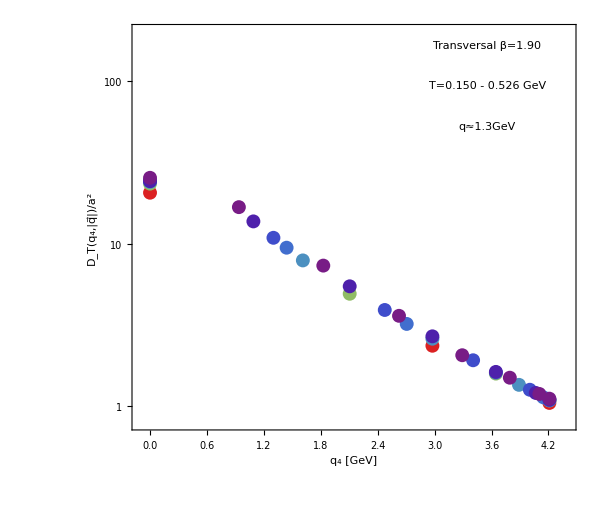

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[If[CurBeta≠7,7,10];;If[CurBeta≠7,7,10]]]}],{CurBeta,1,7}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,4.4},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[1,7,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[1]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[7]],3],SetPrecision[Temp[[1]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[1]][[Table[Min[Flatten@Position[TransversalProcessed[[1]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[1]][[All,3]]][[2;;]]}][[6]],4]],2]],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B190CorrTransVsMuMidPMultiT.pdf",X]
```

B190CorrTransVsMuMidPMultiT.pdf

```mathematica
"b=1.95";
```

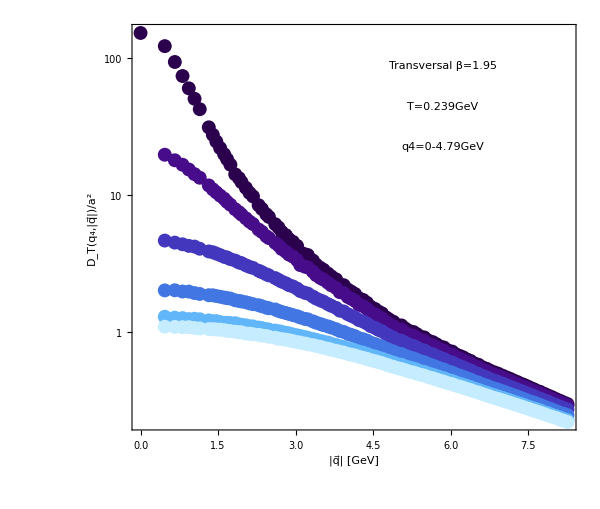

```mathematica
CurBeta=8;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B195CorrTransHighTVspMultiMu.pdf",X]
```

B195CorrTransHighTVspMultiMu.pdf

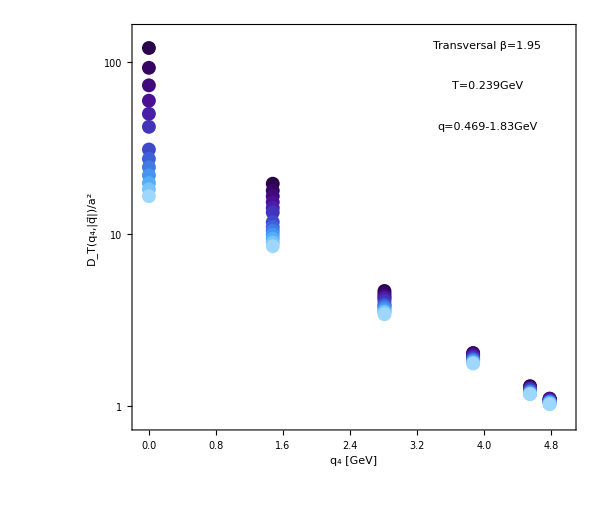

```mathematica
CurBeta=8;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,5},{0.8,150}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B195CorrTransHighTVsmuMultiP.pdf",X]
```

B195CorrTransHighTVsmuMultiP.pdf

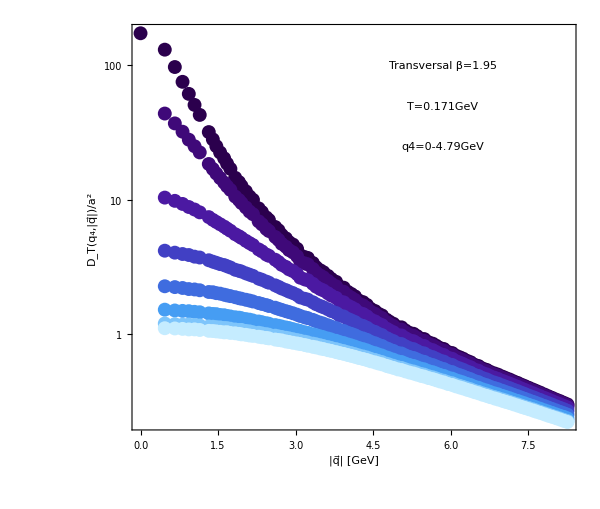

```mathematica
CurBeta=11;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotRange->All,PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B195CorrTransLowTVspMultiMu.pdf",X]
```

B195CorrTransLowTVspMultiMu.pdf

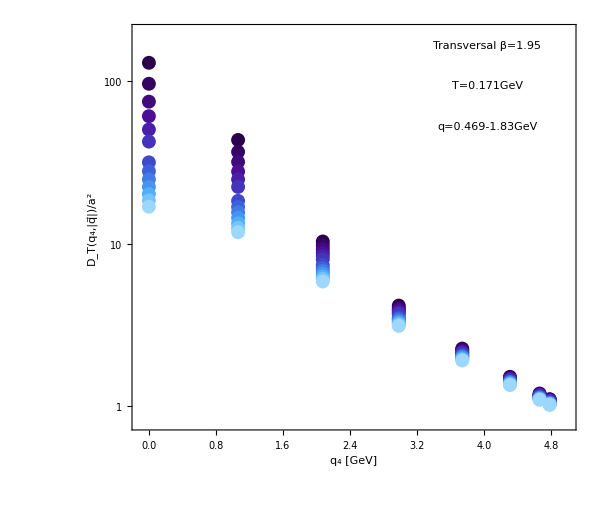

```mathematica
CurBeta=11;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,5},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B195CorrTransLowTVsmuMultiP.pdf",X]
```

B195CorrTransLowTVsmuMultiP.pdf

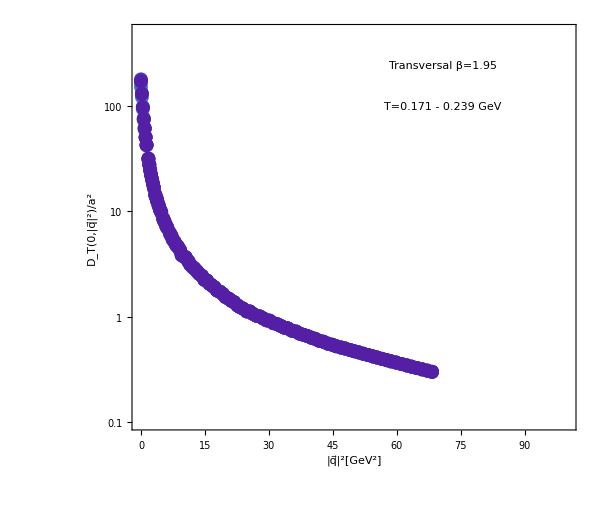

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Table[TransversalProcessed[[b]][[Flatten@Position[TransversalProcessed[[b]][[All,1]],0],{5,6,7}]],{b,8,11}],Frame->{True,True,False,False},PlotRange->{{-0.1,100},{0.1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[8,11,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗|^2[GeV^2]","D_T(0,|q⃗|^2)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[11]],3],SetPrecision[Temp[[8]],3]  ],Scaled[{0.7,0.8}]]},22]]
```

```mathematica
Export["B195CorrTransVsp2MultiT.pdf",X]
```

B195CorrTransVsp2MultiT.pdf

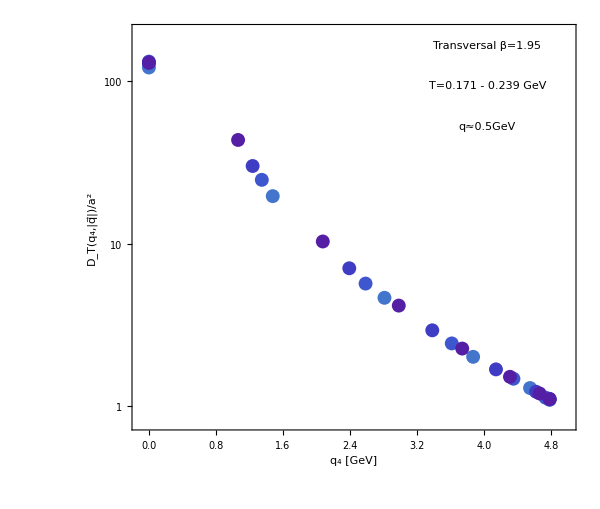

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;2]]}],{CurBeta,8,11}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,5},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[8,11,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[8]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[11]],3],SetPrecision[Temp[[8]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[8]][[Table[Min[Flatten@Position[TransversalProcessed[[8]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[8]][[All,3]]][[2;;]]}][[1]],4]],1]],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B195CorrTransVsMuLowPMultiT.pdf",X]
```

B195CorrTransVsMuLowPMultiT.pdf

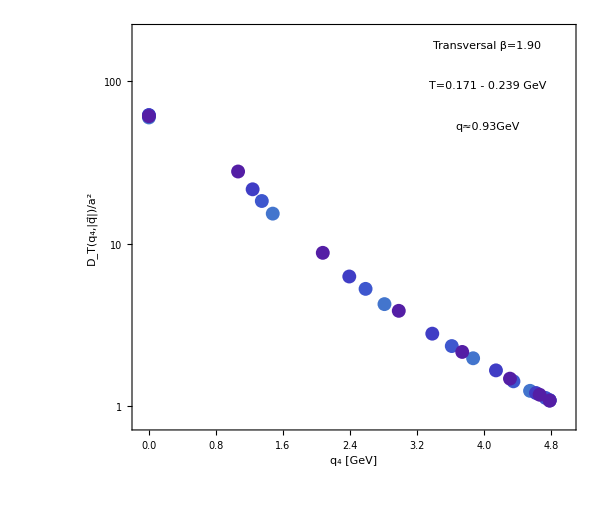

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[5;;5]]}],{CurBeta,8,11}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,5},{0.8,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[8,11,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[2]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[11]],3],SetPrecision[Temp[[8]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[8]][[Table[Min[Flatten@Position[TransversalProcessed[[8]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[8]][[All,3]]][[2;;]]}][[4]],4]],2]],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B195CorrTransVsMuMidPMultiT.pdf",X]
```

B195CorrTransVsMuMidPMultiT.pdf

```mathematica
"b=2.10";
```

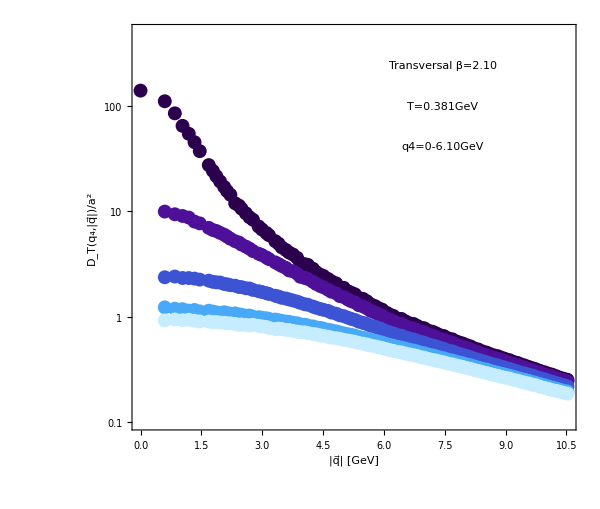

```mathematica
CurBeta=14;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotRange->{All,{0.1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B210CorrTransHighTVspMultiMu.pdf",X]
```

B210CorrTransHighTVspMultiMu.pdf

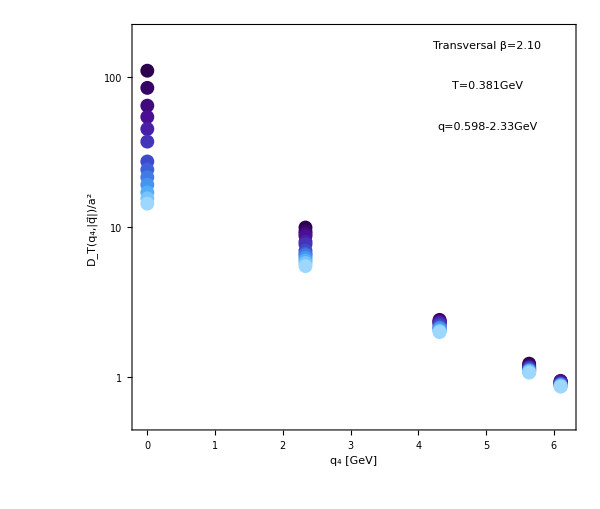

```mathematica
CurBeta=14;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,6.2},{0.5,200}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B210CorrTransHighTVsmuMultiP.pdf",X]
```

B210CorrTransHighTVsmuMultiP.pdf

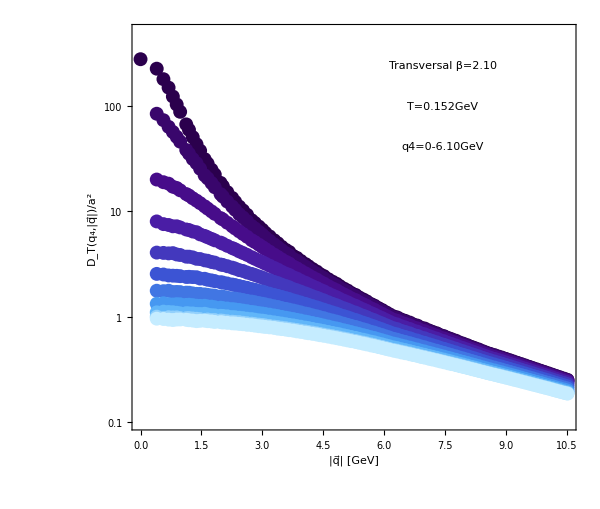

```mathematica
CurBeta=21;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,1]],l],{4,6,7}]],{l,0,NtVals[[CurBeta]]/2}],Frame->{True,True,False,False},PlotRange->{All,{0.1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/(NtVals[[CurBeta]]/2)]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗| [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.7,0.8}]],Text[ToString@StringForm["q4=``-``GeV",SetPrecision[0,3],SetPrecision[TransversalProcessed[[CurBeta]][[Floor[NtVals[[CurBeta]]/2]+2,2]],3]    ],Scaled[{0.7,0.7}]]},22]]
```

```mathematica
Export["B210CorrTransLowTVspMultiMu.pdf",X]
```

B210CorrTransLowTVspMultiMu.pdf

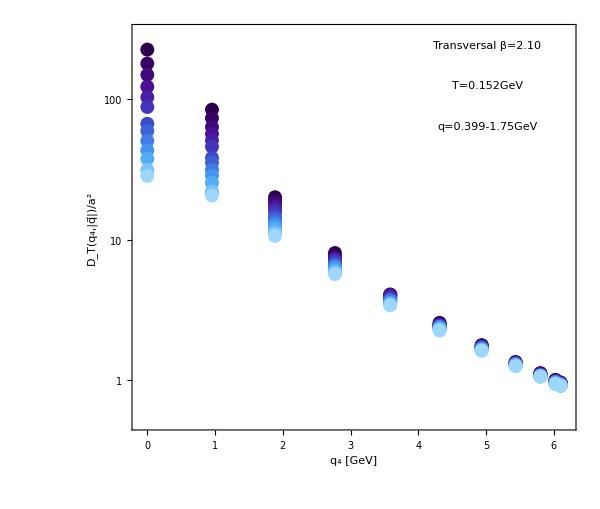

```mathematica
CurBeta=21;
MyColorScheme="DeepSeaColors";X=ErrorListLogPlot[ Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;14]]}],Frame->{True,True,False,False},PlotRange->{{-0.1,6.2},{0.5,300}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@Range[0,1,1/13]},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[CurBeta]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=``GeV",SetPrecision[Temp[[CurBeta]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q=``-``GeV",SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[1]],4]],3],SetPrecision[TransversalProcessed[[CurBeta]][[Table[Min[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[2;;]]}][[14]],4]],3]    ],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B210CorrTransLowTVsmuMultiP.pdf",X]
```

B210CorrTransLowTVsmuMultiP.pdf

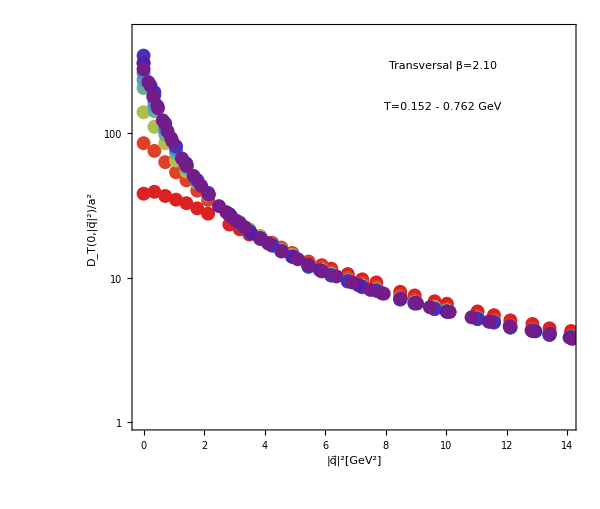

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Table[TransversalProcessed[[b]][[Flatten@Position[TransversalProcessed[[b]][[All,1]],0],{5,6,7}]],{b,12,21}],Frame->{True,True,False,False},PlotRange->{{-0.1,14},{1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[12,21,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗|^2[GeV^2]","D_T(0,|q⃗|^2)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[21]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[21]],3],SetPrecision[Temp[[12]],3]  ],Scaled[{0.7,0.8}]]},22]]
```

```mathematica
Export["B210CorrTransVsp2MultiTZoom.pdf",X]
```

B210CorrTransVsp2MultiTZoom.pdf

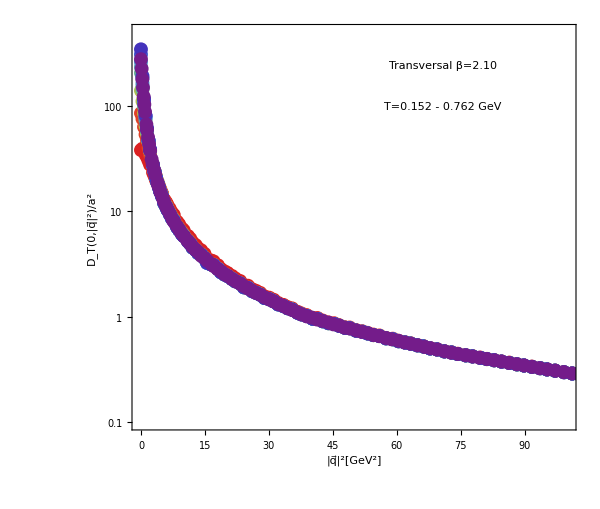

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Table[TransversalProcessed[[b]][[Flatten@Position[TransversalProcessed[[b]][[All,1]],0],{5,6,7}]],{b,{12,13,14,15,16,17,18,19,21}}],Frame->{True,True,False,False},PlotRange->{{-0.1,100},{0.1,500}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[{12,13,14,15,16,17,18,19,21}]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"|q⃗|^2[GeV^2]","D_T(0,|q⃗|^2)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[21]]],Scaled[{0.7,0.9}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[21]],3],SetPrecision[Temp[[12]],3]  ],Scaled[{0.7,0.8}]]},22]]
```

```mathematica
Export["B210CorrTransVsp2MultiT.pdf",X]
```

B210CorrTransVsp2MultiT.pdf

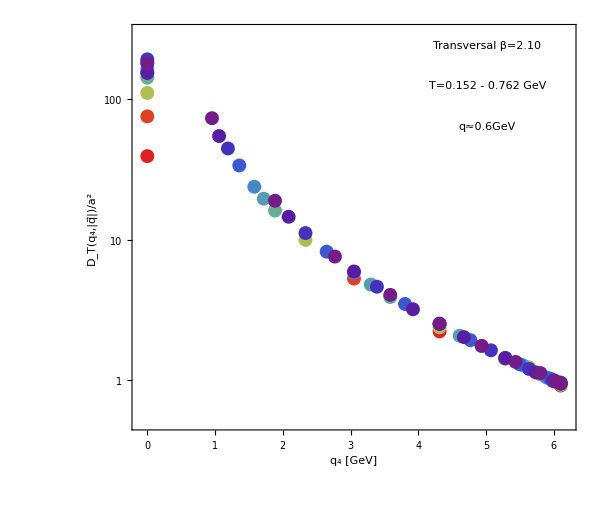

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[If[CurBeta<20,2,If[CurBeta==20,4,3]];;If[CurBeta<20,2,If[CurBeta==20,4,3]]]]}],{CurBeta,12,21}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,6.2},{0.5,300}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[12,21,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[12]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[21]],3],SetPrecision[Temp[[12]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[12]][[Table[Min[Flatten@Position[TransversalProcessed[[12]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[12]][[All,3]]][[2;;]]}][[1]],4]],1]],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B210CorrTransVsMuLowPMultiT.pdf",X]
```

B210CorrTransVsMuLowPMultiT.pdf

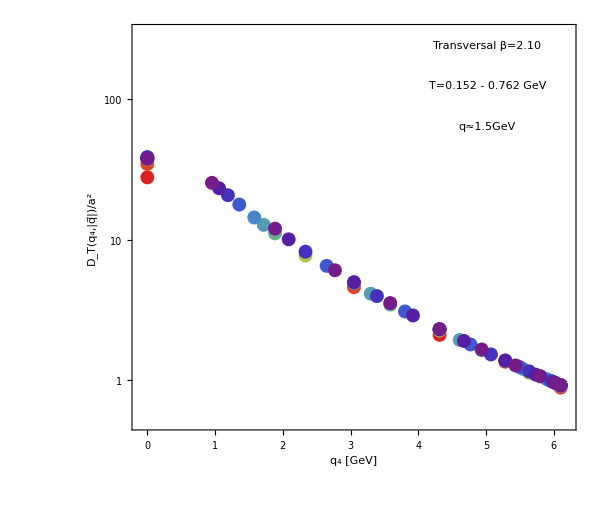

```mathematica
MyColorScheme="Rainbow";X=ErrorListLogPlot[ Flatten[Table[Table[TransversalProcessed[[CurBeta]][[Flatten@Position[TransversalProcessed[[CurBeta]][[All,3]],l],{2,6,7}]],{l,DeleteDuplicates[TransversalProcessed[[CurBeta]][[All,3]]][[If[CurBeta<20,7,If[CurBeta==20,13,12]];;If[CurBeta<20,7,If[CurBeta==20,13,12]]]]}],{CurBeta,12,21}],1],Frame->{True,True,False,False},PlotRange->{{-0.1,6.2},{0.5,300}},PlotStyle->Thread@{AbsolutePointSize[10],ColorData[MyColorScheme]/@((Temp[[Range[12,21,1]]]-MinTmpAll)/(MaxTmpAll-MinTmpAll))},FrameStyle->Directive[FontSize->25,Thickness->0.004, FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,FrameLabel->{"q_4 [GeV]","D_T(q_4,|q⃗|)/a^2"},ImageSize->{600,500},Method->{"AxesInFront" -> False},
Epilog->Style[{Text[ToString@StringForm["Transversal β=``", BetaLatValsP[[12]]],Scaled[{0.8,0.95}]],Text[ToString@StringForm["T=`` - `` GeV ",SetPrecision[Temp[[21]],3],SetPrecision[Temp[[12]],3]  ],Scaled[{0.8,0.85}]],Text[ToString@StringForm["q≈``GeV",SetPrecision[TransversalProcessed[[12]][[Table[Min[Flatten@Position[TransversalProcessed[[12]][[All,3]],j]],{j,DeleteDuplicates[TransversalProcessed[[12]][[All,3]]][[2;;]]}][[6]],4]],2]],Scaled[{0.8,0.75}]]},22]]
```

```mathematica
Export["B210CorrTransVsMuMidPMultiT.pdf",X]
```

B210CorrTransVsMuMidPMultiT.pdf